```mathematica
data1=Import["/home/tony/Workspace/local/benchmark/packet_1.csv"];
data2=Import["/home/tony/Workspace/local/benchmark/packet_2.csv"];
data3=Import["/home/tony/Workspace/local/benchmark/packet_3.csv"];
data4=Import["/home/tony/Workspace/local/benchmark/packet_4.csv"];
data5=Import["/home/tony/Workspace/local/benchmark/packet_5.csv"];
data6=Import["/home/tony/Workspace/local/benchmark/packet_6.csv"];
data7=Import["/home/tony/Workspace/local/benchmark/packet_7.csv"];
data8=Import["/home/tony/Workspace/local/benchmark/packet_8.csv"];
```

```mathematica
data1Time=Transpose[data1][[1]];
data2Time=Transpose[data2][[1]];
data3Time=Transpose[data3][[1]];
data4Time=Transpose[data4][[1]];
data5Time=Transpose[data5][[1]];
data6Time=Transpose[data6][[1]];
data7Time=Transpose[data7][[1]];
data8Time=Transpose[data8][[1]];
data1OH=Transpose[data1][[2]];
data2OH=Transpose[data2][[2]];
data3OH=Transpose[data3][[2]];
data4OH=Transpose[data4][[2]];
data5OH=Transpose[data5][[2]];
data6OH=Transpose[data6][[2]];
data7OH=Transpose[data7][[2]];
data8OH=Transpose[data8][[2]];
```

```mathematica
dataTime=Transpose[{data1Time,data2Time,data3Time,data4Time,data5Time,data6Time,data7Time,data8Time}];
dataOH=Transpose[{data1OH,data2OH,data3OH,data4OH,data5OH,data6OH,data7OH,data8OH}];
dataSpeed=(2^20*8)/(dataTime/1000000);
dataOHSpeed=(2^20*8)/((dataTime-dataOH)/1000000);
meanTime=Table[Mean[dataSpeed[[i]]],{i,1,12}];
meanOHTime=Table[Mean[dataOHSpeed[[i]]],{i,1,12}];
SDTime=Table[StandardDeviation[dataSpeed[[i]]],{i,1,12}];
mean=ListLinePlot[meanTime, PlotStyle->Blue];
meanOH=ListLinePlot[meanOHTime,PlotStyle->Red];
SDMin=ListLinePlot[meanTime-SDTime,PlotStyle->{Blue,Dashed}];
SDMax=ListLinePlot[meanTime+SDTime,PlotStyle->{Blue,Dashed}];
```

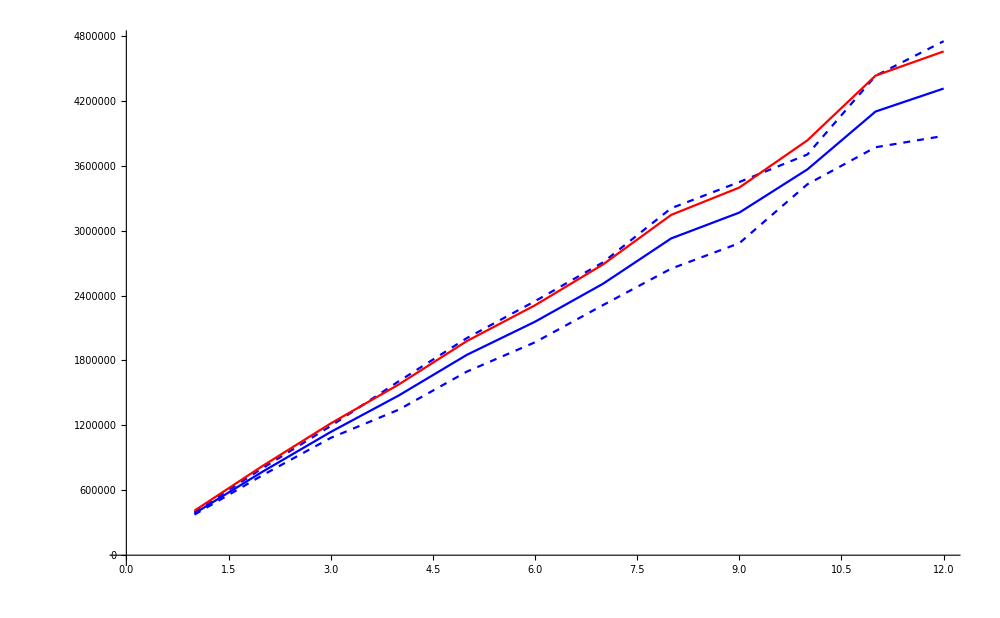

```mathematica
Show[SDMax,SDMin,mean,meanOH,ImageSize->1000]
```